```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@AbsoluteOptions[g,PlotRange],Sequence@@Options[g,Epilog]]
```

/home/zack/cantera/ratematrix

test

{100.,53,325}

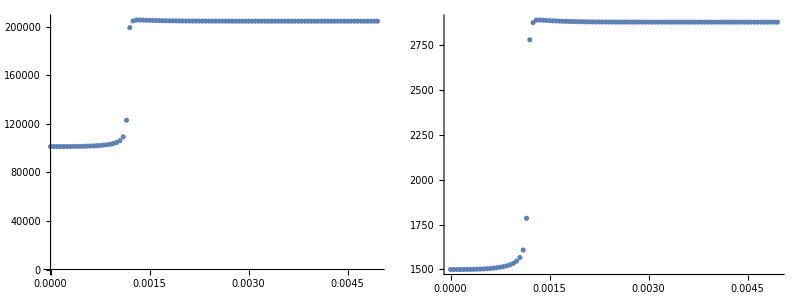

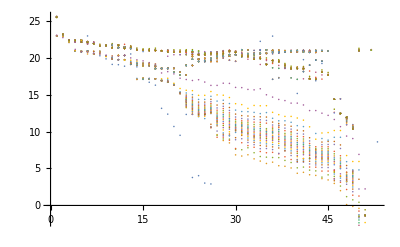

```mathematica
filebase="test"
dat=Import[filebase<>"out.dat"];
{Npoints,ns,nr}=dat[[1,1;;3]]
A=Partition[Partition[BinaryReadList[filebase<>"matrices.npy","Real64"][[17;;-1]],ns],ns];
evals=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2],ns];
evecs=Partition[Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],ns],ns];
frates=Partition[BinaryReadList[filebase<>"frates.npy","Real64"][[17;;-1]],nr];
rrates=Partition[BinaryReadList[filebase<>"rrates.npy","Real64"][[17;;-1]],nr];
Grid[{{ListPlot[Transpose[{dat[[3]],dat[[5]]}]],ListPlot[Transpose[{dat[[3]],dat[[4]]}]]}}]
ListPlot[Log[Abs[evals]]]
```

```mathematica
min=Min[A];
max=Max[A];
Manipulate[MatrixPlot[A[[m]]/(max-min)/2,ColorFunction->(ColorData["TemperatureMap"][1/2+#]&),ColorFunctionScaling->False],{m,1,Length[A],1}]
```

```mathematica
Position[dat[[2]],"OH"]
Position[dat[[2]],"H2O2"]
-0.5*frates[[All,89]]*dat[[5+5,All]]/A[[All,5,8]]
-0.5*frates[[All,89]]*dat[[5+8,All]]/A[[All,8,5]]
```

{{5}}

{{8}}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,1.0192,1.01553,1.01579,1.01673,1.01768,1.01844,1.01901,1.01941,1.01969,1.01986,1.01997,1.02002,1.02004,1.02003,1.01998,1.0199,1.01977,1.01956,1.01924,1.01873,1.01783,1.01605,1.01093,1.00208,1.00154,1.00147,1.00145,1.00144,1.00144,1.00143,1.00143,1.00143,1.00142,1.00142,1.00142,1.00141,1.00141,1.00141,1.00141,1.00141,1.00141,1.00141,1.00141,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,0.982927,0.982739,0.982677,0.982662,0.98267,0.982687,0.98271,0.982741,0.982787,0.982851,0.982938,0.983054,0.983204,0.983397,0.983644,0.983962,0.984373,0.984915,0.985649,0.986686,0.98826,0.990995,0.997522,1.00169,1.0015,1.00146,1.00145,1.00144,1.00144,1.00143,1.00143,1.00142,1.00142,1.00142,1.00142,1.00141,1.00141,1.00141,1.00141,1.00141,1.00141,1.00141,1.00141,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014,1.0014}

```mathematica
Position[dat[[2]],"O"]
Position[dat[[2]],"H2"]
Position[dat[[2]],"H"]
Position[dat[[2]],"OH"]
-0.5*frates[[All,3]]*dat[[5+1,All]]/A[[All,1,3]]
-0.5*frates[[All,3]]*dat[[5+3,All]]/A[[All,3,1]]
0.5*rrates[[All,3]]*dat[[5+2,All]]/A[[All,5,2]]
```

{{3}}

{{1}}

{{2}}

{{5}}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,-0.00693281,-0.0077999,-0.00918282,-0.0110407,-0.0134477,-0.0165333,-0.0204337,-0.0252724,-0.0311582,-0.0381921,-0.046482,-0.0561638,-0.0674276,-0.0805503,-0.0959409,-0.11421,-0.136298,-0.163724,-0.199167,-0.24801,-0.323686,-0.476997,-1.47747,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{0.,2.50076×10^-7,4.61067×10^-7,7.69288×10^-7,1.1762×10^-6,1.6961×10^-6,2.34955×10^-6,3.15044×10^-6,4.10882×10^-6,5.24265×10^-6,6.5873×10^-6,8.20203×10^-6,0.0000101769,0.0000126444,0.0000158012,0.0000199498,0.0000255788,0.0000335301,0.0000453767,0.0000643885,0.0000984769,0.000171845,0.00039858,0.00299647,0.49365,0.336908,0.314667,0.310426,0.30873,0.307487,0.306409,0.305449,0.304596,0.303841,0.303174,0.302587,0.302072,0.301622,0.301227,0.300884,0.300584,0.300323,0.300096,0.299899,0.299727,0.299579,0.29945,0.299338,0.299241,0.299157,0.299084,0.299021,0.298967,0.29892,0.298879,0.298844,0.298813,0.298787,0.298764,0.298744,0.298727,0.298712,0.298699,0.298688,0.298678,0.29867,0.298663,0.298657,0.298651,0.298647,0.298643,0.298639,0.298636,0.298634,0.298631,0.298629,0.298628,0.298626,0.298625,0.298624,0.298623,0.298622,0.298621,0.298621,0.29862,0.29862,0.298619,0.298619,0.298619,0.298619,0.298618,0.298618,0.298618,0.298618,0.298618,0.298618,0.298618,0.298618,0.298617,0.298617}

```mathematica
Position[dat[[2]],"HO2"]
Position[dat[[2]],"C3H7"]
-0.5*frates[[All,323]]*dat[[5+7,All]]/A[[All,7,50]]
-0.5*frates[[All,323]]*dat[[5+50,All]]/A[[All,50,7]]
```

{{7}}

{{50}}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,0.00928596,0.00928608,0.00928612,0.0092861,0.00928605,0.00928596,0.00928582,0.00928564,0.0092854,0.00928509,0.0092847,0.00928423,0.00928364,0.00928292,0.00928202,0.0092809,0.00927947,0.00927759,0.00927504,0.0092714,0.00926569,0.00925523,0.00923077,0.00940295,0.0094336,0.00943835,0.00943867,0.00943839,0.00943806,0.00943776,0.00943748,0.00943724,0.00943702,0.00943683,0.00943666,0.00943652,0.00943639,0.00943627,0.00943618,0.00943609,0.00943601,0.00943595,0.00943589,0.00943584,0.0094358,0.00943576,0.00943573,0.0094357,0.00943568,0.00943566,0.00943564,0.00943562,0.00943561,0.0094356,0.00943559,0.00943558,0.00943557,0.00943557,0.00943556,0.00943556,0.00943555,0.00943555,0.00943554,0.00943554,0.00943554,0.00943554,0.00943553,0.00943553,0.00943553,0.00943553,0.00943553,0.00943553,0.00943553,0.00943553,0.00943553,0.00943553,0.00943553,0.00943553,0.00943553,0.00943553,0.00943552,0.00943552,0.00943552,0.00943552,0.00943552,0.00943552,0.00943552,0.00943552,0.00943552,0.00943552,0.00943552,0.00943552,0.00943552,0.00943552,0.00943552,0.00943552,0.00943552,0.00943552,0.00943552}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,-0.00150992,-0.00112814,-0.00102086,-0.000981541,-0.000973476,-0.00098582,-0.00101377,-0.00105489,-0.00110855,-0.00117563,-0.00125827,-0.00135993,-0.00148583,-0.00164412,-0.00184798,-0.00212009,-0.00250231,-0.00308032,-0.00405837,-0.00606536,-0.0123917,0.265205,0.0117973,0.00940288,0.00943342,0.00943814,0.00943845,0.00943817,0.00943784,0.00943754,0.00943726,0.00943701,0.0094368,0.0094366,0.00943643,0.00943629,0.00943616,0.00943604,0.00943594,0.00943586,0.00943578,0.00943571,0.00943566,0.00943561,0.00943557,0.00943553,0.0094355,0.00943547,0.00943544,0.00943542,0.0094354,0.00943539,0.00943537,0.00943536,0.00943535,0.00943534,0.00943534,0.00943533,0.00943532,0.00943532,0.00943531,0.00943531,0.00943531,0.0094353,0.0094353,0.0094353,0.0094353,0.0094353,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529,0.00943529}